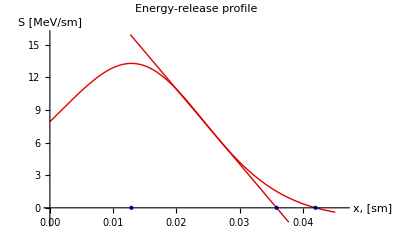

0.0129018

0.00053299

0.0420425

0.0358718

```mathematica
Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity];
AtomicMass:=29.918738317022;Charge:=14.300403999999999; MaterialDensity:=2.834;
Gh=(AtomicMass/Charge)/MaterialDensity;
Rpq[En_]:=Gh*0.482*0.421*Power[En,1.265-0.0954*Log[En]];
pq[xv_,En_]:=xv/Rpq[En];
Pq[xv_,En_]=1.437/(({Cosh[0.95*(2.295*pq[xv,En]-1)]}^1.8)*(0.5+1/(2.7-2.295*pq[xv,En])));
Qq[xv_,En_]:=En/Rpq[En]*Pq[xv,En];
gg[en_]=0.073261 en^(1.265-0.0954 Log[en]) *Gh;
(*gn[en_]=(3.2586918469271406)*0.07326 en^(1.265-0.0954 Log[en]) *Gh//Simplify;*)
gn[en_]=Gh*0.23873176470588234 en^(1.265-0.0954 Log[en]);
(*gl[en_]=Gh*0.2396385 en^(1.265-0.0954 Log[en])*(0.85);*)
gl[en_]=Gh*0.203692725 en^(1.265-0.0954 Log[en]);
LL[xp_,en_]=InterpolatingPolynomial[{{gg[en]*1.55,Qq[gg[en]*1.55,en]},{gg[en]*2,Qq[gg[en]*2,en]}},xp];

eneg:=0.35;
Plot[{Qq[a,eneg],LL[a,eneg]},{a,0,3.5*gg[eneg]},PlotRange->{{0,3.6*gg[eneg]},{-0.1*FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}],1.2FindMaxValue[Qq[x,eneg],{x,0,3.6*gg[eneg]}]}},ColorFunction->Function[{x,y},If[y≥0,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick,Epilog->{PointSize[Large],Blue,Point[{gg[eneg],0}],Point[{gn[eneg],0}],Point[{gl[eneg],0}],

Text["density"MaterialDensity,{0.75,FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text["A"AtomicMass ,{0.75,0.9*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}],
Text["Z"Charge,{0.75,.8*FindMaxValue[Qq[x,eneg],{x,0,3.5*gg[eneg]}]}]   },AxesLabel->{"x, [sm]","S [MeV/sm]"} ,PlotLabel->"Energy-release profile" ]
gg[eneg]
r1=0.025;
r2=0.033;
(*gg[eneg]*Pi*MaterialDensity*(r2^2-r1^2)/100*)
MaterialDensity*1000*Pi*(r2^2-r1^2)*(gg[eneg]/100)//N
gn[eneg]
gl[eneg]

Clear[Gh]; Clear[gg]; Clear[AtomicMass]; Clear[Charge]; Clear[MaterialDensity]; ClearAll;
```

```mathematica
5.32989646743421*^-4
```

0.00053299

```mathematica
14.577*2.834*0.0129*Pi
```

1.6742